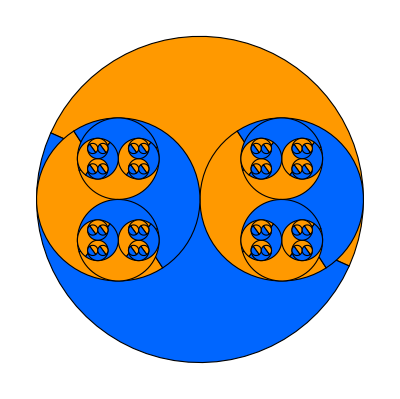
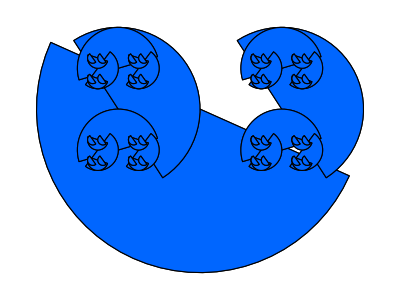
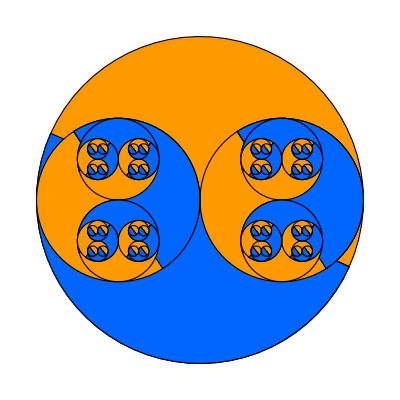
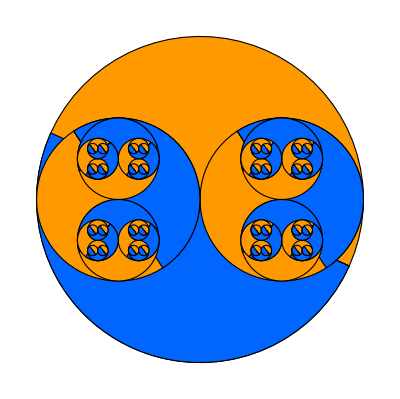
{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
diskfractal[start_]:=Module[{numcircles,radius,iter,lastIndex,arr,p,k,size,chunk,angleincr},
f1[x_,y_,r_,p_] := {x+r/2*Cos[p],y+r/2*Sin[p],r/2,p+angleincr};
f2[x_,y_,r_,p_] := {x-r/2*Cos[p],y-r/2*Sin[p],r/2,p+angleincr};
f1b[x_,y_,r_,p_,i_] := {x+r/2*Cos[p],y+r/2*Sin[p],r/2,If[Mod[i,2]==1, p+angleincr,p-angleincr],i};
f2b[x_,y_,r_,p_,i_] := {x-r/2*Cos[p],y-r/2*Sin[p],r/2,If[Mod[i,2]==1, p+angleincr,p-angleincr],i};
numcircles = 2; (*keep at 2*)radius = 20;iter = 5;
angleincr = Pi/2;
(*Print["Phase = ",phase]*)
size = 1+∑_(e=1)^iter numcircles^e;
arr = ConstantArray[0,{size,4}];
arr[[1]] = {0,0,radius,start};
p=1;
For[i=1, i<iter+1,i++,
chunk = numcircles^(i-1);
lastIndex=1+∑_(e=0)^(i-1) numcircles^e;
(*p= lastIndex -1*Boole[i-2<=0]- (numcircles^(i-2)-1)*Boole[i-2>0]; best one for original:+start*(i^(2/3))*)
For[k=lastIndex,k<(lastIndex+numcircles*chunk),k+=numcircles,
(*uncomment the 2 lines below for normal roatation (every iteration rotates in the same direction_ *)
(*arr[[k]]        = f1[arr[[p,1]],arr[[p,2]],arr[[p,3]],arr[[p,4]]+start];
arr[[k+1]] = f2[arr[[p,1]],arr[[p,2]],arr[[p,3]],arr[[p,4]]+start];
*)
(*uncomment the 3 lines below for the rotation to alternate iterations *)
prev = arr[[p,4]];
pow = 1.8;
arr[[k]]        = f1b[arr[[p,1]],arr[[p,2]],arr[[p,3]],If[Mod[i,2]==1,prev+start*i,prev-start*i],i];
arr[[k+1]] = f2b[arr[[p,1]],arr[[p,2]],arr[[p,3]],If[Mod[i,2]==1,prev+start*i,prev-start*i],i];
p++;
];
p=lastIndex;
];(*end of iteration for loop, not end of the function,*)

(*Circles split by two colors*)
hue1=0.1;(*.09/.65 is orange/blue and .17/.78 is yellow/purple*)
hue2=0.6;
disks = Table[{EdgeForm[Black],
Hue[ hue1],
Disk[{arr[[i,1]],arr[[i,2]]},arr[[i,3]],{arr[[i,3]]-Pi/2+start,arr[[i,3]]+Pi/2}+start],
Hue[ hue2],
Disk[{arr[[i,1]],arr[[i,2]]},arr[[i,3]],{arr[[i,3]]+Pi/2+start,arr[[i,3]]+3Pi/2+start}]},
{i,size}];


(*Solid Circles by iteration;
getiter[index_]:={
sum=0;
count=0;
While[sum<index,
sum = ∑_(e=0)^count numcircles^e;
count++;];
{count}};
disks = Table[{EdgeForm[Black],
Hue[ If[Mod[getiter[i][[1,1]],2]==0,{0,0,1},{0,0,0}]],
Disk[{arr[[i,1]],arr[[i,2]]},arr[[i,3]]]},
{i,size}];*)

(*output graphics or array values*)
{Graphics[{disks}]}
(*{arr}*)
](*end of the module for the fractal function*)
(* a factor of Pi/2 to fit the first iter *)
{diskfractal[0],diskfractal[2Pi],diskfractal[8Pi],diskfractal[12Pi],diskfractal[16Pi]}
(*{diskfractal[4Pi],diskfractal[16Pi]}*)
Animate[diskfractal[seed],{seed,4Pi,16Pi},AnimationRate->0.01,AnimationRunning->False,ShrinkingDelay->500]
```

```mathematica
(*Printing images*)
seedstep=.002
j=0
For[seed=0Pi,seed<Pi,seed+=seedstep,
pic = diskfractal[seed];
SetDirectory[FileNameJoin[{NotebookDirectory[],"simple2"}]];
Export[StringJoin["Fractal_pic",ToString[j],".png"],pic, ImageSize->800];
j++;
]
```

0.002

0

```mathematica
Pi/.002//N
```

1570.8

```mathematica
(*Finding the perfect loop*)
baseline = diskfractal[4Pi];
other = diskfractal[seed];
seed = 6*Pi;
difference = 100;
While[difference>.000000001,
difference = 0;
other = diskfractal[seed];
For[u=1,u<Length[baseline],u++,
difference =difference + baseline[[1,1]]- other[[1,1]]+baseline[[1,2]]- other[[1,2]] +baseline[[1,4]] -other[[1,4]];
]
seed=seed+2Pi;
];
Print[seed]
```

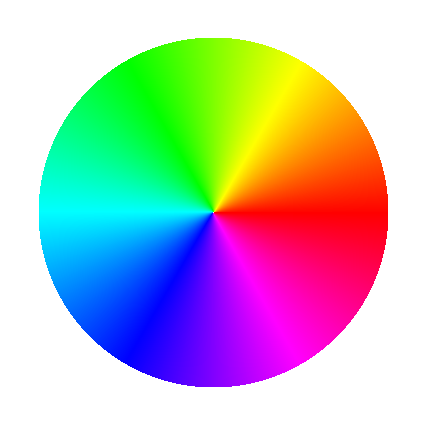

```mathematica
Graphics[Table[{Hue[z/1000],Disk[{0,0},1,{2Pi/1000*(z-1),2Pi/1000*z} ] },{z,1000}]
]
```

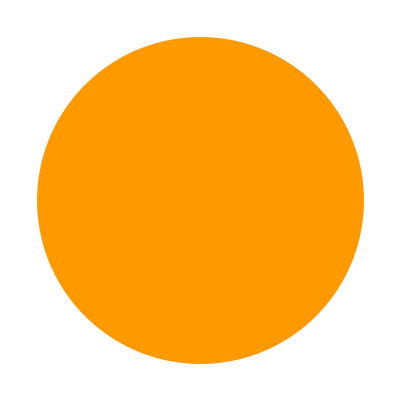
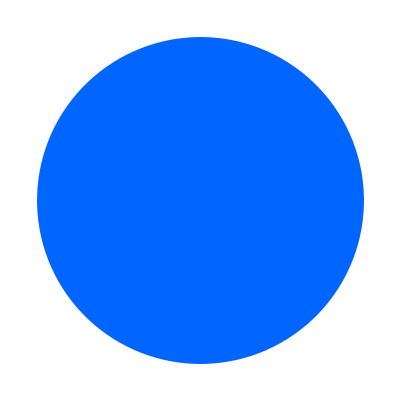
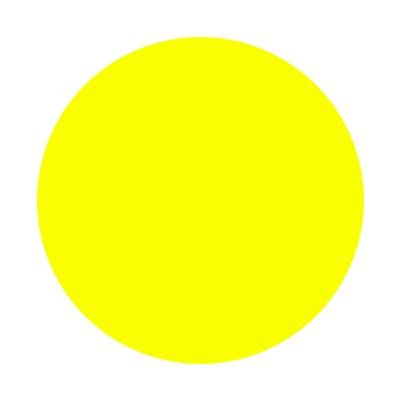
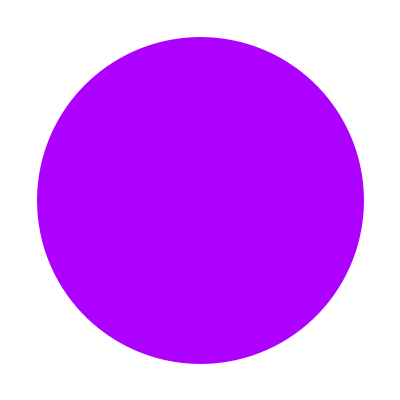
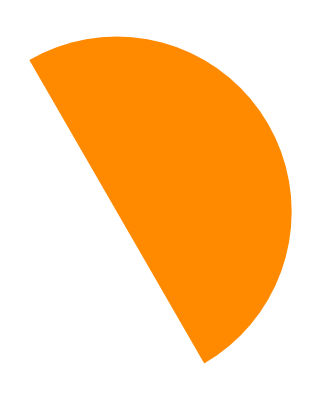
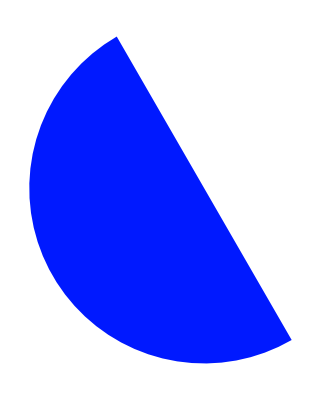


```mathematica
angle = Pi/6;
hue2={0,0,0};
{Graphics[{Hue[.1],Disk[]}],
Graphics[{Hue[.6],Disk[]}],
Graphics[{Hue[.17],Disk[]}],
Graphics[{Hue[.78],Disk[]}],
Graphics[{Hue[.09],Disk[{0,0},1,{angle+Pi/2,angle-Pi/2}]}],
Graphics[{Hue[.65],Disk[{0,0},1,{angle+Pi/2,angle+3Pi/2}]}],
Graphics[{Hue[hue2],Disk[]}]

}
```